```mathematica
ω0[u0_,d_]:=2(1-(d^2 √(1+d^2))/((d^2+(u0-1)^2)^(3/2)))
```

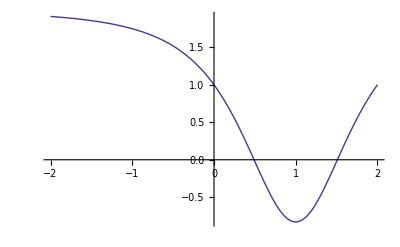

```mathematica
Plot[ω0[x,1],{x,-2,2}]
```

```mathematica
FullSimplify[Solve[ω0[x,1]==0,x]]
```

{{x→1-√(-1+2^(1/3))},{x→1+√(-1+2^(1/3))}}

```mathematica
1. x/.First[%]
```

0.490175